```mathematica
Integrate[2Exp[-1/2 Exp[2 x] + x-1/2 Log[2 π]],{x,-∞,∞}]
```

1

```mathematica
n=3;
σx=100;
```

```mathematica
A2=n^2+1-2Log[σx];
N[A2]
```

0.78966

```mathematica
x0=NSolve[A2-Exp[2x]/σx^2+2x==0,x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-0.394807},{x→5.86915}}

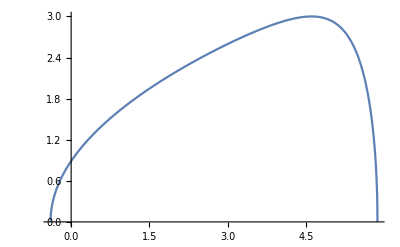

```mathematica
Plot[√(A2-Exp[2x]/σx^2+2x),{x,x/.x0[[1]],x/.x0[[2]]}]
```

```mathematica
n=3;
σx=1;
```

```mathematica
A2=n^2+1-2Log[σx];
N[A2]
```

10.

```mathematica
x0=NSolve[A2-Exp[2x]/σx^2+2x==0,x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-4.99998},{x→1.26398}}

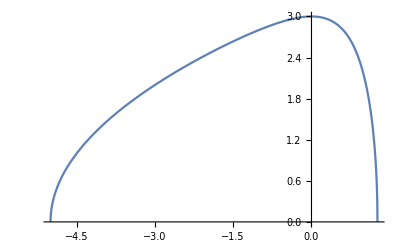

```mathematica
Plot[√(A2-Exp[2x]/σx^2+2x),{x,x/.x0[[1]],x/.x0[[2]]}]
```